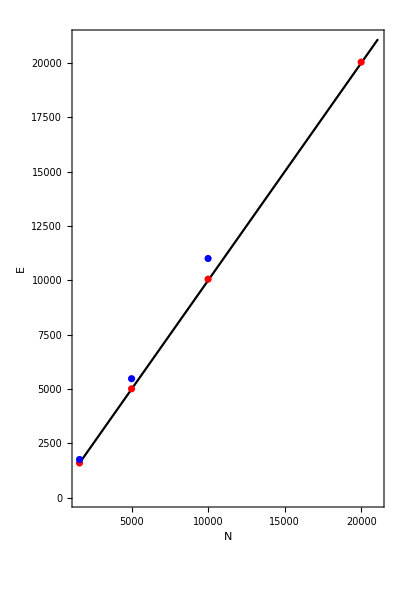

```mathematica
ideal1={{1600,1603.73},{5000,5014.9678},{10000,10060.6316},{20000,20043.1}};(*10^4+10^4 MD steps*)
ideal2={{1600,1762.6},{5000,5480.8},{10000,11010.7},{20000,21934.4}};(*5 10^3+5 10^3 MD steps*)
Show[Plot[ x,{x,1500,21100},PlotStyle->Black],ListPlot[{ideal1,ideal2},PlotStyle->{Red,Blue}],Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm["N"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]},AspectRatio->1.5]
```

-0.56514+0.00155919 x+7.36445×10^-8 x^2

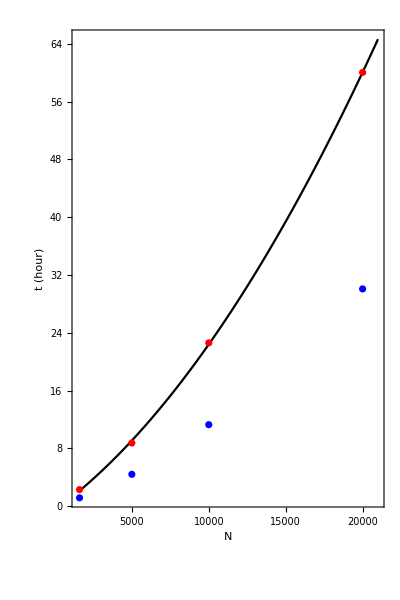

```mathematica
time1={{1600,8218/3600},{5000,31437/3600},{10000,81350/3600},{20000,216162/3600}};(*10^4+10^4 MD steps*)
time2={{1600,4108/3600},{5000,15828/3600},{10000,40569/3600},{20000,108266/3600}};(*5 10^3+5 10^3 MD steps*)
fit=Fit[time1,{1,x,x^2},x]
Show[Plot[ fit,{x,1500,21000},PlotRange->All,PlotStyle->Black],ListPlot[{time1,time2},PlotStyle->{Red,Blue}],Frame->True,FrameLabel->{{HoldForm["t (hour)"],None},{HoldForm["N"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]},AspectRatio->1.5]
```